# 38: Conjugate Gradients (CG)

We saw that Arnoldi and all sorts of other stuff became simpler for symmetric matrices. In particular, we could build a expanding orthogonal basis for the Krylov space  	
	𝒦_n(A,b):=span({b,A.b,A^2.b,…,A^(n-1).b})
without orthogonalizing against all the previous directions.  The simplified process to build the tridiagonal H and the orthogonal Q was renamed the Lanczos process. Code to iteratively compute the diagonal α and subdiagonal β entries of H and the orthogonal Q is below.

A very specific simplification is possible when solving A.x=b and A is Symmetric a positive definite.  It is the original Krylov space solver and is very effective when applicable and appropriately preconditioned.

## Lanczos Code

```mathematica
LanczosInit[A_][q1_]:= Module[{v,α1,β1,q2},
v=A.q1;
α1=q1.v;
v = v - α1 q1;
β1=Norm[v];
q2=v/β1;
{{q1,q2}ᵀ,{{α1},{β1}}}
]
Lanczos[A_][{Q_,{α_,β_}}]:= Module[{m,n,qn,v,αn,βn,qNew},
{m,n}=Dimensions[Q];
qn=Q⟦All,n⟧;
v=A.qn;
αn=qn.v;
v=v-β⟦n-1⟧ Q⟦All,n-1⟧-αn qn;
βn=Norm[v];
qNew=v/βn;
{ArrayFlatten[({{Q, {qNew}ᵀ}})],{Append[α,αn],Append[β,βn]}}
]
```

Testing.  Note the preliminary initialization!

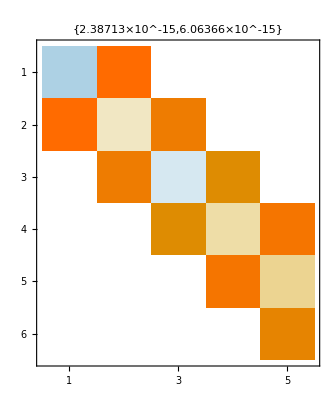

```mathematica
m=123;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
q1=Normalize[RandomReal[{-1,1},m]];
{Q1,{α1,β1}}=LanczosInit[A][q1];
n=5;
{Q,{α,β}}=Nest[Lanczos[A],{Q1,{α1,β1}},n-1];
H=SparseArray[{Band[{1,1}]->α,Band[{2,1}]->β,Band[{1,2}]->Drop[β,-1]}];
MatrixPlot[H,
PlotLabel->Map[Norm,{Qᵀ.Q-IdentityMatrix[n+1],A.Q⟦All,1;;n⟧-Q.H}]]
```

## Solving A.x=b with Conjugate Gradients.

From now on we are going to assume that A ϵ ℝ^(m×m) is Symmetric and Positive Definite abbreviated to SPD and write x_∞ for the solution satisfying A.x_∞=b.  As a reminder positive definite means x.A.x>0 unless x=0.  As a result SPD means ||x(||)_(CG(A)):=√(x.A.x) is a norm!   Minimizing the residual using this specially tailored norm gives the very simple and effective conjugate gradient algorithm.

### Residual Computation and Cost Function ϕ.

The first thing to do is to work out what is special about this way of measuring the residual.  Take a look
  	||x-x_∞(||)_(CG(A))^2=(x-x_∞).A.(x-x_∞)=(x-x_∞).(A.x-A.x_∞)=(x-x_∞).(A.x-b)=x.A.x-x.b-x_∞.A.x+x_∞.b
  Maybe nothing stand out right now but remember A=Aᵀ so x_∞.A.x=(Aᵀ.x_∞).x=(A.x_∞).x=b.x so 
  	||x-x_∞(||)_(CG(A))^2=x.A.x-x.b-x_∞.A.x+x_∞.b=x.A.x-2 x.b+x_∞.b=2(1/2 x.A.x - b.x)+constant.
  Define
  	ϕ(x)=1/2 x.A.x - b.x
 and note that the readily computable derivative
  	Dϕ(x)=A.x - b=-(b-A.x)=-r(x)
is just the negative of residual.  In words, we can solve A.x=b by minimizing ϕ. In symbols, x_∞=argmin ϕ(x).

One way to minimize a convex function is to head straight down hill from any starting point until you hit bottom (in that direction) then turn to the new straight downhill direction and repeat the process until you get to the overall minimum.  Straight downhill from a point x_n is the direction 
	-Dϕ(x_n)=b-A.x_n=r_n.  
which is just the residual r_n=b-A.x_n. Along this search direction we have a single variable quadratic in α 
	g(α):=ϕ(x_n+α r_n)=1/2(x_n+α r_n).A.(x_n+α r_n)-b.(x_n+α r_n)
with derivative
	g'(α)=(x_n+α r_n).A.r_n-b.r_n=(A.x_n-b).r_n+α r_n.A.r_n=α r_n.A.r_n-r_n.r_n.
Solve g'(α)=0 give the minimum at 
	α_(n+1)=r_n.r_n/(r_n.A.r_n)
which defines our improved approximate solution
	x_(n+1)=x_n+α_n r_n.
If r(x_(n+1))=-Dϕ(x_(n+1))=0 then x_(n+1) is the global minimum. If  r(x_(n+1))≠0 continuing the iterative process will further reduce ϕ(x).

This is a weighted steepest descent method for ϕ(x) with an "exact" line search! It is steepest descent because it searches along the negative gradient -Dϕ(x_n)!  It is an exact line search because α_n gives the exact minimum along the search (steepest descent) direction!

A direct computation explicitly gives the explicit formula for the improvement 
	ϕ(x_n)-ϕ(x_(n+1))=1/2(r_n.r_n)^2/(r_n.A.r_n).
Not surprisingly the update conditions have geometric interpretations.  Since r_n is tangent to the ϕ contour at x_(n+1) we have r_n⊥r_(n+1). The g'(α_(n+1))=0 condition can be interpreted as r_n⊥(r_n-α_(n+1) A.r_n)
	g'(α)=α r_n.A.r_n-r_n.r_n=-r_n.(r_n-α A.r_n).
I am going to display these because they are going to be recognizable in the code below.

### Algorithm 38.1

Conjugate gradients (Algorithm 38.1) is simply this exact line search minimization starting from the predetermined  initial guess x_0=OverVector[0].  Here is the pseudo code from the text

Conjugate Gradients
x_0=0, r_0=b, p_0=r_0
for n in 1, 2, 3, ...
	α_n=(r_(n-1).r_(n-1))/(p_(n-1).A.p_(n-1))
	x_n=x_(n-1)+α_n p_(n-1)
	r_n=r_(n-1)-α_n A.p_(n-1)
	β_n=(r_n.r_n)/(r_(n-1).r_(n-1))
	p_n=r_n+β_n p_(n-1)

Lets look at the start of this process in 2D.

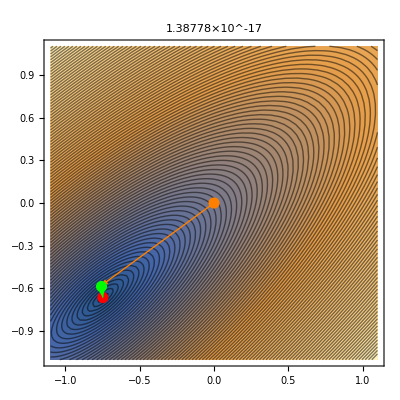

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ; 
CGNorm[A_][x_]:=√(x.A.x)
xInf= Normalize[RandomReal[{-1,1},m]];
(* Initialization *)
b=A.xInf;
r0 =b;p0=r0;x0=0*b;
α0=(r0.r0)/(p0.A.p0);
(* n=1 *)
α1 = (r0.r0)/(p0.A.p0);
x1 =x0 + α1 p0;
r1=r0-α1 A.p0;
β1 = (r1.r1)/(r0.r0);
p1=r1 + β1 p0;
(* n=2 just the start *)
α2 = (r1.r1)/(p1.A.p1);
x2 =x1 + α2 p1;
r2=r1-α2 A.p1;
(* Pic *)
ContourPlot[CGNorm[A][{x,y}-xInf],
{x,-1.1,1.1},
{y,-1.1,1.1},
Contours->100,
AspectRatio->Automatic,
Epilog->{PointSize[0.02],
{Red,Point[xInf]},
{Orange, Point[x0], Arrow[{x0,x1}]},
{Green, Point[x1], Arrow[{x1,x2}]}
},
PlotLabel->Norm[r2]
]
```

Lets try to look at the start of this process in 3D.

```mathematica
m=3;
A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ; 
CGNorm[A_][x_]:=√(x.A.x)
xInf= Normalize[RandomReal[{-1,1},m]];
(* Initialization *)
b=A.xInf;
r0 =b;p0=r0;x0=0*b;
α0=(r0.r0)/(p0.A.p0);
(* n=1 *)
α1 = (r0.r0)/(p0.A.p0);
x1 =x0 + α1 p0;
r1=r0-α1 A.p0;
β1 = (r1.r1)/(r0.r0);
p1=r1 + β1 p0;
(* n=2 just the start *)
α2 = (r1.r1)/(p1.A.p1);
x2 =x1 + α2 p1;
r2=r1-α2 A.p1;
(* Pic *)
ϕVals=Map[CGNorm[A],{x0-xInf,x1-xInf,x2-xInf}]
Show[
ContourPlot3D[CGNorm[A][{x,y,z}-xInf],
{x,-1.1,1.1},
{y,-1.1,1.1},
{z,-1.1,1.1},
ContourStyle->Opacity[0.5],
Contours->ϕVals,
AspectRatio->Automatic,
PlotLabel->Norm[r2]
],
Graphics3D[{PointSize[0.02],
{Red,Point[xInf]},
{Orange,Point[x0],Arrow[{x0,x1}]},
{Green,Point[x1],Arrow[{x1,x2}]}}]]
```

{0.35491,0.197877,0.168406}

-Graphics3D-

### CG Code

A single step directly (the only modification is to store the matrix vector multiplication) from pseudo code.

```mathematica
CGStep[A_][{xIn_,rIn_,pIn_}]:=Module[{ApIn=A.pIn,α,β,xOut,rOut,pOut},
α=(rIn.rIn)/(pIn.ApIn);
xOut=xIn+α pIn;
rOut=rIn - α ApIn;
β = (rOut.rOut)/(rIn.rIn); 
pOut=rOut+β pIn;
{xOut,rOut,pOut}]
```

Note, essentially all the work per step is the matrix vector-multiplication.  Find the thing that could be made more efficient! Tell me why I do not care very much!

Import an SPD A 
	https://math.nist.gov/MatrixMarket/data/Harwell-Boeing/bcsstruc1/bcsstk05.html
from Matrix Market.

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc1/bcsstk05.mtx.gz"]
(*MatrixPlot[A]*)
m=Length[A];
MaxIter=22;
(* Create an identifiable RHS *)
xInf=Table[Cos[0.1 i],{i,m}];
ListPlot[xInf];
b=A.xInf;
{x0,r0,p0}={0*b, b,b};
xrpData=NestList[CGStep[A],{x0,r0,p0},MaxIter];
TabView[{
"x"->MatrixPlot[xrpData⟦All,1⟧],
"r"->MatrixPlot[xrpData⟦All,2⟧],
"p"-> MatrixPlot[xrpData⟦All,3⟧]
}]
TabView[{
"||x-x_∞(||)_(CG (A))"->ListLogPlot[Map[CGNorm[A][#-xInf]&,xrpData⟦All,1⟧]],
"||x-x_∞(||)_2"->ListLogPlot[Map[Norm[#-xInf]&,xrpData⟦All,1⟧]],
"||r||"->ListLogPlot[Map[Norm,xrpData⟦All,2⟧]]
}]
```

SparseArray[…]

123

123

Slow but very steady is what I would say here. Remember, preconditioners are essential!

## Convergence

We already know from either the derivation or the code that

The CG norm of the residual ||x_n-x_∞(||)_(CG(A))^2=(x_n-x_∞).A.(x_n-x_∞)=2ϕ(x_n)+constant.

We also know know from either the derivation or the code that

r_(n+1).r_n=0

p_(n+1).A.p_n=0

and an induction argument shows that as longs the computation does not converge i.e. r_n=0

Residuals r_n are orthogonal i.e. r_j.r_n=0 for j<n

Search directions p_n are A conjugate i.e. p_j.A.p_n=0 for j<n

We can reinterpret this in terms of the Krylov Space
	𝒦_n=span{x_1,x_2,…,x_n}=span{p_1,p_2,…,p_n}=span{r_0,r_1,…,r_(n-1)}
which are all equal to the standard Krylov space
	𝒦_n(b,A)=span{b,A.b,…,A^(n-1).b}

Theorem 38.2 says in part that in exact arithmetic the CG algorithm converges monotonically in the CG norm and terminates in n steps with n≤m. This is not surprising! We have seen the monotonicity, it runs out of dimensions to search after m steps, and the only thing that can go wrong r_k=0 would indicate convergence.

The more useful part of Theorem 38 says that x_n minimizes x_n=argmin_𝒦_n||x-x_∞(||)_(CG(A)).  To see this plug x=x_n+Δx∈𝒦_n into the tailored norm and expand to get 
	||x-x_∞(||)_(CG(A))^2=(x_n-x_∞+Δx).A.(x_n-x_∞+Δx)=(x_n-x_∞).A.(x_n-x_∞)+Δx.A.Δx+2(x_n-x_∞).A.Δx
The conjugacy built into the algorithm ensures the last term is zero so 
	||x-x_∞(||)_(CG(A))^2=(x_n-x_∞+Δx).A.(x_n-x_∞+Δx)=(x_n-x_∞).A.(x_n-x_∞)+Δx.A.Δx≥(x_n-x_∞).A.(x_n-x_∞)
Since A is SPD and the last term is strictly positive unless Δx=0

In floating point arithmetic the algorithm can stall i.e. stop making useful progress. In practice, like all other iterative algorithms CG really needs preconditioned.

## Optimality

Just like the other Krylov algorithms we have looked at CG has an optimality property for polynomials.  Not surprisingly CG is optimal in the tailored norm. Theorem 38.3 shows that CG constructs the polynomial that minimizes ||p_n(A)(x_∞-x_0)(||)_(CG(A)) over the set of polynomials with p(0)=1 where our initial guess x_0is always the zero vector. The trick to seeing this is to use the orthogonal eigen basis {v_1,v_2,…,v_m} for A and note that 
	||p(A)(x_∞-x_0)(||)_(CG(A))^2=∑_(j=1)^m a_j^2 λ_j * (p(λ_j))^2 and ||(x_∞-x_0)(||)_(CG(A))^2=∑_(j=1)^m a_j^2 λ_j
where x_∞-x_0=∑_(j=1)^m a_j v_j.  Just like before we get a useful expression for the appropriate scaled relative error
	(||x_∞-x_n(||)_(CG(A)))/(||x_∞-x_0(||)_(CG(A)))=minp∈𝒫_n (||p(A)(x_∞-x_0)(||)_(CG(A)))/(||x_∞-x_0(||)_(CG(A)))≤minp∈𝒫_n max_(λ∈Λ(A))|p(λ)|.

This has lots of useful consequences for matrices with clustered eigenvalues. The book presents two very different results.

The first concerns  eigenvalues clustered as tightly as possible and there are only n "distinct" eigenvalues: in practice this result essentially holds for n "tight" eigenvalue clusters.  What it says is that in this case CG converges in less than n-steps. In practice, CG resolves clusters of eigenvalues simultaneously.

The second expresses the worst possible convergence rate for a spectrum with eigenvalues λ spread between 0<λ_min≤λ≤λ_max in terms of the condition number κ=λ_max/λ_min. The worst possible convergence rate is
	 (||x_∞-x_n(||)_(CG(A)))/(||x_∞-x_0(||)_(CG(A)))≤2((√κ-1)/(√κ+1))^n∼(1-2/(√k))^n

### Clustered Examples

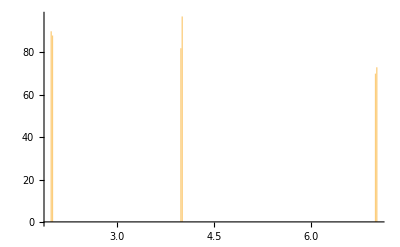

```mathematica
m=500;
ϵ=10^-6;
dist=MixtureDistribution[{1,1,1},
{NormalDistribution[2,ϵ],NormalDistribution[4,2ϵ],NormalDistribution[7,3ϵ]}];
λs=RandomVariate[dist,m];
Q=Orthogonalize[RandomReal[{-1,1},{m,m}]];
A=Q.DiagonalMatrix[λs].Qᵀ;
Histogram[λs,200]
```

```mathematica
xInf=RandomReal[{-1,1},m];
b=A.xInf;
MaxIter=8;
{x0,r0,p0}={0*b, b,b};
xrpData=NestList[CGStep[A],{x0,r0,p0},MaxIter];
TabView[{
"x"->MatrixPlot[xrpData⟦All,1⟧],
"r"->MatrixPlot[xrpData⟦All,2⟧],
"p"-> MatrixPlot[xrpData⟦All,3⟧]
}]
TabView[{
"||x-x_∞(||)_(CG (A))"->ListLogPlot[Map[CGNorm[A][#-xInf]&,xrpData⟦All,1⟧]],
"||x-x_∞(||)_2"->ListLogPlot[Map[Norm[#-xInf]&,xrpData⟦All,1⟧]],
"||r||"->ListLogPlot[Map[Norm,xrpData⟦All,2⟧]]
}]
```

123

123

### Non-Clustered Examples

0.980198

700

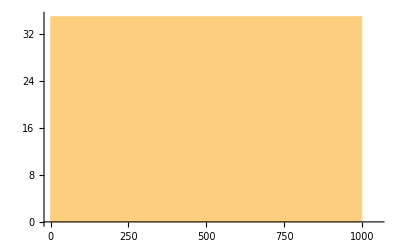

```mathematica
m=700;
{λMin,λMax}={0.1,1000};
κEst=λMax/λMin;
EstRate=(√κEst-1)/(√κEst+1)
λs=Table[λ,{λ,λMin,λMax,(λMax-λMin)/(m-1)}];
Length[λs]
Q=Orthogonalize[RandomReal[{-1,1},{m,m}]];
A=Q.DiagonalMatrix[λs].Qᵀ;
Histogram[λs,25]
```

```mathematica
xInf=RandomReal[{-1,1},m];
b=A.xInf;
MaxIter=100;
{x0,r0,p0}={0*b, b,b};
xrpData=NestList[CGStep[A],{x0,r0,p0},MaxIter];
TabView[{
"x"->MatrixPlot[xrpData⟦All,1⟧],
"r"->MatrixPlot[xrpData⟦All,2⟧],
"p"-> MatrixPlot[xrpData⟦All,3⟧]
}]
TabView[{
"||x-x_∞(||)_(CG (A))"->ListLogPlot[{
Map[CGNorm[A][#-xInf]&,xrpData⟦All,1⟧],
Table[EstRate^n,{n,1,MaxIter}]}],
"||x-x_∞(||)_2"->ListLogPlot[Map[Norm[#-xInf]&,xrpData⟦All,1⟧]],
"||r||"->ListLogPlot[Map[Norm,xrpData⟦All,2⟧]]
}]
```

123

123

## Preconditioners

For CG to make sense we need the iteration matrix to be SPD.  We know exactly two preconditioners: Jacobi and ILU.  The diagonal entries of an SPD matrix must be positive!  In this case, almost all of them are pretty darn big!

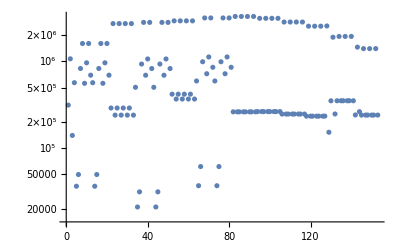

```mathematica
ListLogPlot[Diagonal[A]]
```

To make the iteration modified matrix for CG Symmetric we need to multiply on both sides. If we define 
	S = SparseArray[Diagonal[A]^(-1/2), {m, m}]
so that S^2 is the original Jacobi preconditioner then solving 
	A.x=b ⟺S.A.x=S.b ⟺S.A.S.y=S.b where S.y=x.
Since S is diagonal the matrix S.A.S=S.A.Sᵀ is symmetric and the final step x=S^-1.y to solve for x is very inexpensive.  Lets compare the eigenvalues of (all real and positive) the original and transformed matrices

```mathematica
A=Import[
"https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc1/bcsstk05.mtx.gz"];
m=Length[A];
S=SparseArray[Band[{1,1}]->1/√Normal[Diagonal[A]],{m,m}];SAS=S.A.S; InvS=Inverse[S];
{λA,λSAS}= Map[Eigenvalues,Normal[{A,SAS}]];
{κA,κSAS}=Map[Max[#]/Min[#]&,{λA,λSAS}];
ListLogPlot[{λA,λSAS},
PlotLegends->{"A","SAS"},
PlotLabel->StringForm["Condition Numbers = ``",{κA,κSAS}]
];
(* Create an identifiable Answer and the matching RHS *)
xInf=Table[Cos[0.1 i],{i,m}];
b=A.xInf;
Sb=S.b;
yInf=Inverse[S].xInf;
(* Compute CG data for SAS *)
{y0,r0,p0}={0*Sb, Sb,Sb};
yrpData=NestList[CGStep[SAS],{y0,r0,p0},MaxIter];
xData=Table[y=yrpData⟦i,1⟧;Inverse[S].y,{i,Length[yrpData]}];
TabView[{
"y"->MatrixPlot[yrpData⟦All,1⟧],
"x"->MatrixPlot[xData],
"r"->MatrixPlot[yrpData⟦All,2⟧],
"p"-> MatrixPlot[yrpData⟦All,3⟧]
}]
TabView[{
"||y-y_∞(||)_CG"->ListLogPlot[Map[CGNorm[SAS][#-yInf]&,yrpData⟦All,1⟧],AxesLabel->{"n","||y-y_∞(||)_CG"}],
"||y-y_∞(||)_2"->ListLogPlot[Map[Norm[#-yInf]&,yrpData⟦All,1⟧],AxesLabel->{"n","||y-y_∞(||)_2"}],
"||r||"->ListLogPlot[Map[Norm,yrpData⟦All,2⟧],AxesLabel->{"n","||r||"}]
}]
```

1234

123

Better but not good.  An Incomplete Cholesky (IC)  decomposition A≈Uᵀ.U for SPD matrices analogous to the Incomplete LU (ILU)  decomposition A≈L.U would be useful because we could iterate with 		
	(U^-1)ᵀ.A.(U^-1)≈(U^-1)ᵀ.Uᵀ.U.(U^-1)≈I.  
The no-fill Incomplete Cholesky decomposition produces a upper triangular matrix U with the same sparsity pattern as the input.  We are going to modify our first (row oriented) Cholesky decomposition below to only update the originally non-zero entries.  Here is our old row oriented standard Cholesky.

Book Cholesky (from before)

R=A
for k in 1:m
	for j in k+1:m
		R[j,j:m]=R[j,j:m]-R[k,j:m]*R[k,j]/R[k,k]
	end
	R[k,k:m]=R[k,k:m]/sqrt(R[k,k])
end
triu!(R)

All I really need to do to make it an incomplete Cholesky is modify the inner loop to only update entries of a sparse vector that already exist

```mathematica
v=SparseArray[{Band[{1,1}]->Range[1,4],{2,3}->1.2,{5,1}->2.3},{12,8}];
SAProps=v["Properties"];
TableForm[Table[{p,v[p]},
{p,SAProps}],
TableHeadings->{SAProps,Automatic}]
```

| 1 | 2
AdjacencyLists | AdjacencyLists | 1 | 
2 | 3
3 | 
4 | 
1 | 
 | 
 | 
 | 
 | 
 | 
 | 
 | 
BandWidth | BandWidth | 4
1
ColumnIndices | ColumnIndices | 1
2
3
3
4
1
Density | Density | 0.0625
ExplicitLength | ExplicitLength | 6
ExplicitPositions | ExplicitPositions | 1 | 1
2 | 2
2 | 3
3 | 3
4 | 4
5 | 1
ExplicitValues | ExplicitValues | 1
2
1.2
3
4
2.3
ImplicitValue | ImplicitValue | 0
RowPointers | RowPointers | 0
1
3
4
5
6
6
6
6
6
6
6
6
ReplaceValues | ReplaceValues | SparseArray[…]

```mathematica
{"AdjacencyLists","ColumnIndices","Density","ExplicitLength","ExplicitPositions","ExplicitValues","ImplicitValue","RowPointers","ReplaceValues"}
```

p
SparseArray[…][p]

SparseArray[…]

{1.2,2.3}

{{2},{5}}

{AdjacencyLists,ColumnIndices,Density,ExplicitLength,ExplicitPositions,ExplicitValues,ImplicitValue,RowPointers,ReplaceValues}

SparseArray[…]

```mathematica
R[[k,k;;m]]=R[[k,k;;m]]/Sqrt[R[[k,k]]]
```

```mathematica
R[[k,k;;m]]=R[[k,k;;m]]/Sqrt[R[[k,k]]]
```

```mathematica
IdentityMatrix[12,SparseArray,WorkingPrecision->MachinePrecision]
```

SparseArray[…]

```mathematica
VectorUpdate[v1_,v2_]
```

CholeskyBook[A_]:= Module[{R=A,m=Length[A]},
Do[
Do[
R⟦j,j;;m⟧=R⟦j,j;;m⟧-R⟦k,j;;m⟧ R⟦k,j⟧/R⟦k,k⟧,
{j,k+1,m}];
R⟦k,k;;m⟧=R⟦k,k;;m⟧/√R⟦k,k⟧,
{k,1,m}];
UpperTriangularize[R]]

```mathematica
x=SparseArray[]
```

From Wiki https://en.wikipedia.org/wiki/Incomplete_Cholesky_factorization
Octave

function a = ichol(a)
	n = size(a,1);

	for k=1:n
		a(k,k) = sqrt(a(k,k));
		for i=(k+1):n
		    if (a(i,k)!=0)
		        a(i,k) = a(i,k)/a(k,k);            
		    endif
		endfor
		for j=(k+1):n
		    for i=j:n
		        if (a(i,j)!=0)
		            a(i,j) = a(i,j)-a(i,k)*a(j,k);  
		        endif
		    endfor
		endfor
	endfor

    for i=1:n
        for j=i+1:n
            a(i,j) = 0;
        endfor
    endfor            
endfunction

Incomplete Cholesky (no fill)
for k in 1:n
	a[k,k] = sqrt(a[k,k]);
	A[k+1:n,k] = A[k+1:n,k]/A[k,k]
		for j=(k+1):n
		    for i=j:n
		        if (a(i,j)!=0)
		            a(i,j) = a(i,j)-a(i,k)*a(j,k);  
		        endif
		    endfor
		endfor
	endfor

    for i=1:n
        for j=i+1:n
            a(i,j) = 0;
        endfor
    endfor            
endfunction

Such functions exist but lets see what we can fake up ourself. This problem is small enough that we can compute the Cholesky decomposition which would be the "perfect" preconditioner! As an experiment lets try keeping the first few diagonals

```mathematica
Clear[Ud]
U=CholeskyDecomposition[A];
Id=IdentityMatrix[Length[A]];
Ud[0]=SparseArray[Band[{1,1}]->Diagonal[U,0]];
Ud[n_]:=Ud[n]=Ud[n-1]+SparseArray[Band[{1,n+1}]->Diagonal[U,n],{m,m}]
```

```mathematica
TabView[
Table[
UInv=Inverse[Ud[n]];
n->MatrixPlot[Ud[n],
PlotLabel->{Norm[A-Ud[n]ᵀ.Ud[n],"Frobenius"]/Norm[A,"Frobenius"],Norm[UInvᵀ.A.UInv-Id,"Frobenius"]}
],{n, 0,32}]
]
```

123456789101112131415161718192021222324252627282930313233

The spectrum (remember the set of all the eigenvalues) of the iteration matrices are very important.  The bad news is that we would need to go quite far out from the diagonal to get a “tight” spectrum.

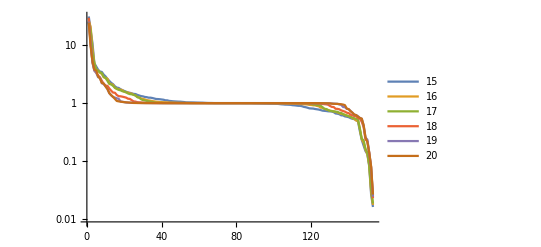

```mathematica
{nMin,nMax}={15,20};
ListLogPlot[
Table[
UInv=Inverse[Ud[n]];
Eigenvalues[UInvᵀ.A.UInv],{n, nMin,nMax}],
Joined->True,PlotLegends->Range[nMin,nMax]]
```

A better idea is to see which entries are (or maybe should be big).  Since A is SPD the diagonal entries are positive and can perform a symmetric scaling to make all the diagonal entries 1.  This is just the symmetric variant of the Jacobi preconditioner w looked at before.

```mathematica
S=SparseArray[Band[{1,1}]->Normal[Diagonal[A]]^(-1/2)];
A0=S.A.S;ListPlot[Diagonal[A0]];
```

So now 
	A_0=Id + A_1
where all diagonal entries of A_1 are zero!  The power series (called a Neumann series in this context) gives
	(A_0)^-1=(Id+A_1)^-1=Id-A_1+A_1.A_1-A_1.A_1.A_1+…  
which converges fast (we do not need to add up many terms) if A_1 is small.  It is not obvious how to make this a symmetric preconditioner suitable for CG. What we want is an approximation R≈(A_0)^(-1/2) so that R.A_0.R≈Id.  The power series
	(A_0)^(-1/2)=(Id+A_1)^(-1/2)=Id-1/2 A_1+3/8 A_1^2-5/16 A_1^3+35/128 A_1^4+…
converges fast provided A_1is small.  Lets see how these would do as preconditioners.

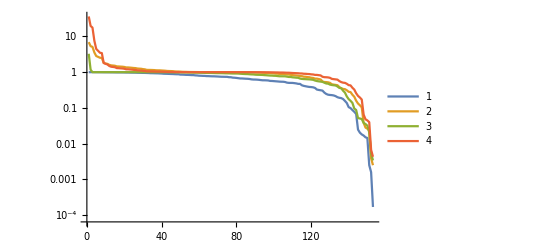

```mathematica
Id=SparseArray[Band[{1,1}]->1,Dimensions[A0]];
A1=A0-Id;
R[1]=Id-1/2 A1;
R[2] = R[1]+3/8 A1.A1;
R[3]=R[2]-5/16 A1.A1.A1;
R[4]=R[3]+35/128 A1.A1.A1.A1;
TabView[{
"A0"->MatrixPlot[A0],
"R[1]"->MatrixPlot[R[1]],
"R[2]"->MatrixPlot[R[2]],
"R[3]"->MatrixPlot[R[3]],
"R[4]"->MatrixPlot[R[4]]
}];
λs=Table[
Eigenvalues[R[n].A0.R[n]],{n,1,4}];
ListLogPlot[λs,Joined->True,PlotLegends->Automatic]
```

So this thought process suggests that we might be able to use the sparsity patterns of powers of A as templates for approximate inverses.  This is exactly what the ILU we saw before does.  It is slightly more complicated for a symmetric Cholesky.

## Sparsity Patterns

Suppose we want to find an upper triangular U with a given sparsity pattern that satisfies
	U.A.Uᵀ≈I
We need to

{1-x/2,1-x/2+(3 x^2)/8,1-x/2+(3 x^2)/8-(5 x^3)/16,1-x/2+(3 x^2)/8-(5 x^3)/16+(35 x^4)/128,1-x/2+(3 x^2)/8-(5 x^3)/16+(35 x^4)/128-(63 x^5)/256,1/(√(1+x))}

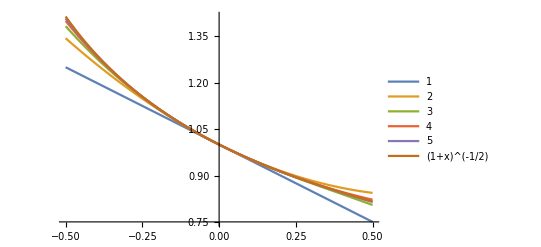

```mathematica
Hmm=Append[Table[
Normal[Series[(1+x)^(-1/2),{x,0,n}]],
{n,5}],(1+x)^(-1/2)]
Plot[Hmm,{x,-1/2,1/2},
PlotLegends->Append[Range[1,5],"(1+x)^(-1/2)"]]
```

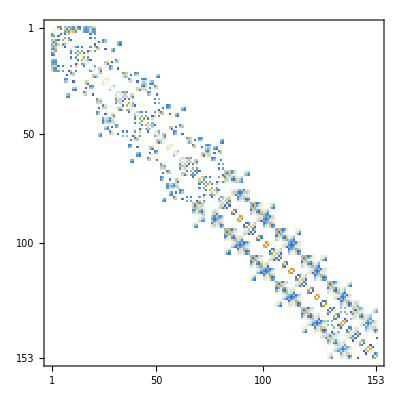

{9.11739,10.3018,11.1174}

```mathematica
Id=IdentityMatrix[Length[A0]];
A1=A0-Id; 

MatrixPlot[A1]

Map[Norm[#,"Frobenius"]&,{A1,A1.A1,A1.A1 -A1.A1.A1}]
```

```mathematica
Series[(1+x)^-1,{x,0,4}]
```

1-x+x^2-x^3+x^4+O[x]^5

```mathematica
Serei
```

```mathematica
U2=SparseArray[{
Band[{1,1}]->Diagonal[U],
Band[{1,2}]->Diagonal[U,1],
Band[{1,2}]->Diagonal[U,2]}]
{InvU,InvU2}=Map[Inverse,{U,U2}];
TabView[{
"U"->MatrixPlot[U,PlotLabel->Norm[A-Uᵀ.U]/Norm[A]],
"Λ(U^-1.A.(U^-1)ᵀ"->ListLogPlot[Eigenvalues[InvUᵀ.A.InvU ],PlotRange->All],
"U2"->MatrixPlot[U2,PlotLabel->Norm[A-U2ᵀ.U2]/Norm[A]],
"Λ(U2^-1.A2.(U2^-1)ᵀ"->ListLogPlot[Eigenvalues[InvU2ᵀ.A.InvU2 ],PlotRange->All]
}]
```

SparseArray[…]

SparseArray[…]

1234

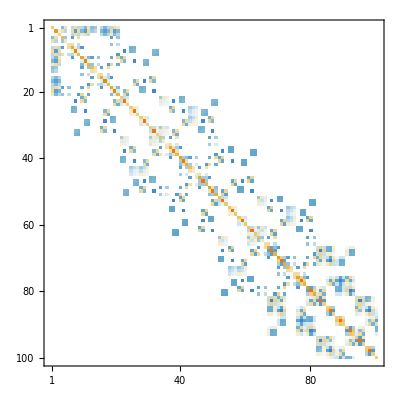

```mathematica
MatrixPlot[A⟦1;;100,1;;100⟧]
```

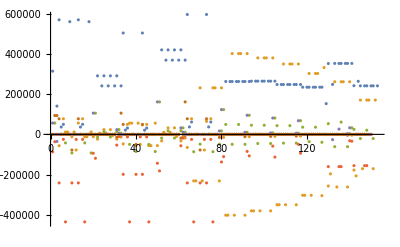

```mathematica
ListPlot[Table[Diagonal[A,i],{i,0,5}]]
```

```mathematica
AHat=SparseArray[ Band]
```

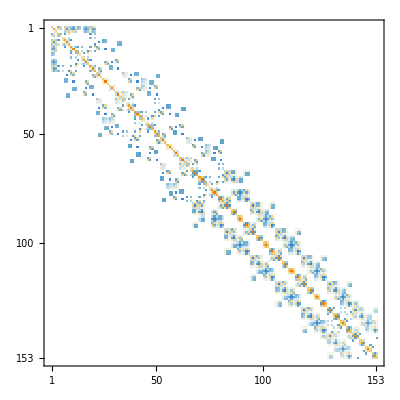

```mathematica
L=Ch
```

```mathematica
Options[SparseArray`SparseMatrixILU]
```

{SparseArray`FillIn→Automatic,Method→ILUT,SparseArray`PermutationTolerance→Automatic,Tolerance→Automatic}